```mathematica
(*
l=64;
ll=ToString[l];
d=0.221654;
dd=ToString[d];
histd[d][l]={};
dat[l]={};
Do[

ii=ToString[i];
data[i][l]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/Ising/ising-EMHL-l"<>ll<>"-k"<>dd<>"-run"<>ii<>".txt",{Number,Number,Number,Number,Number,Number}];
dat[l]=Join[dat[l],data[i][l]];
,{i,{1}}
]
dat[l]=Sort[dat[l],#1[[1]]<#2[[1]]&];

hi[l]=Table[{dat[l][[All,1]][[i]],dat[l][[All,2]][[i]]},{i,1,Length[dat[l]]}];
*)
```

```mathematica
(*
l=32;
his[l]={};
data[l]={};
For [i=1,i<Length[hi[l]] , i++,
If[hi[l][[All,1]][[i]]==hi[l][[All,1]][[i+1]],
his[l]=Append[his[l],{hi[l][[All,1]][[i]],(hi[l][[All,2]][[i]]+hi[l][[All,2]][[i+1]])}]; 
data[l]=Append[data[l],{dat[l][[All,1]][[i]],(dat[l][[All,2]][[i]]+dat[l][[All,2]][[i+1]]),
(dat[l][[All,3]][[i]]*dat[l][[All,2]][[i]]+dat[l][[All,3]][[i+1]]*dat[l][[All,2]][[i+1]])/(dat[l][[All,2]][[i]]+dat[l][[All,2]][[i+1]]),(dat[l][[All,4]][[i]]*dat[l][[All,2]][[i]]+dat[l][[All,4]][[i+1]]*dat[l][[All,2]][[i+1]])/(dat[l][[All,2]][[i]]+dat[l][[All,2]][[i+1]]),
(dat[l][[All,5]][[i]]*dat[l][[All,2]][[i]]+dat[l][[All,5]][[i+1]]*dat[l][[All,2]][[i+1]])/(dat[l][[All,2]][[i]]+dat[l][[All,2]][[i+1]]),
(dat[l][[All,6]][[i]]*dat[l][[All,2]][[i]]+dat[l][[All,6]][[i+1]]*dat[l][[All,2]][[i+1]])/(dat[l][[All,2]][[i]]+dat[l][[All,2]][[i+1]])}];
i = i+1;
 , his[l]=Append[his[l],{hi[l][[All,1]][[i]],hi[l][[All,2]][[i]]}];

data[l]=Append[data[l],{dat[l][[All,1]][[i]],dat[l][[All,2]][[i]],dat[l][[All,3]][[i]],dat[l][[All,4]][[i]],dat[l][[All,5]][[i]],dat[l][[All,6]][[i]]}];

]
]
*)
```

```mathematica
k=0.221654;
dd=ToString[k];
Do[
ll=ToString[l];
data[l]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/Ising/ising-EMHL-l"<>ll<>"-k"<>dd<>".txt",{Number,Number,Number,Number,Number,Number}];
his[l]=Table[{data[l][[All,1]][[i]],data[l][[All,2]][[i]]},{i,1,Length[data[l]]}];
,{l,{8,12,16,24,32,48,64,96}}]
```

```mathematica
Length[his[32]]
```

2317

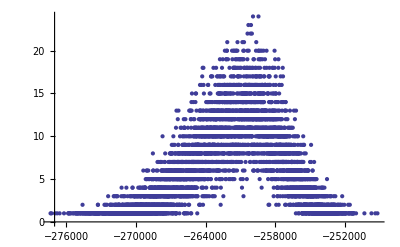

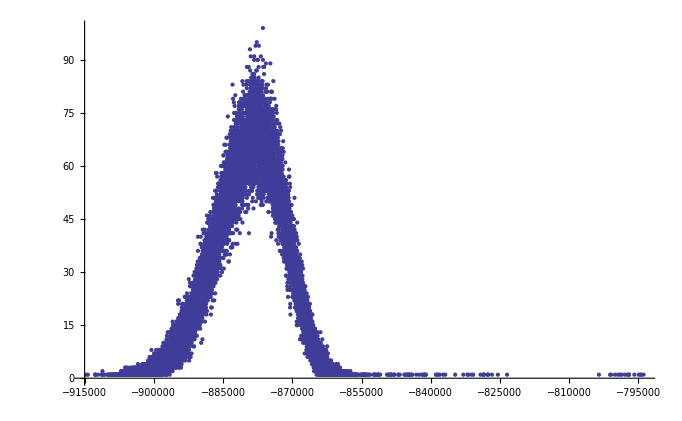

```mathematica
ListPlot[hi[64],PlotRange->Full]
ListPlot[his[96],PlotRange->Full]
```

```mathematica
Do[
e[l]=data[l][[All,1]];
h[l]=data[l][[All,2]];
m[l]=data[l][[All,3]];
am[l]=data[l][[All,4]];
m2[l]=data[l][[All,5]];
m4[l]=data[l][[All,6]];

,{l,{8,12,16,24,32,48,64,96}}]
```

```mathematica
ClearAll[M2E]
```

```mathematica
k0=0.221654;

Do[
En[l]={};
E2[l]={};
M[l]={};
absM[l]={};
M2[l]={};
M4[l]={};
U[l]={};

absME[l]={};
M2E[l]={};
c[l]={};


For[k=0.22075,k<0.22225,k += 0.00002,
z[k][l]=Sum[his[l][[All,2]][[i]]*Exp[(k0-k)*his[l][[All,1]][[i]]],{i,1,Length[his[l]]}];
hist[k][l]=Table[{his[l][[All,1]][[i]],his[l][[All,2]][[i]]*Exp[(k0-k)*his[l][[All,1]][[i]]]/z[k][l]},{i,1,Length[his[l]]}];
En[l]=Append[En[l],{k,Sum[hist[k][l][[All,2]][[i]]*e[l][[i]],{i,1,Length[hist[k][l]]}]}];
M[l]=Append[M[l],{k,Sum[hist[k][l][[All,2]][[i]]*m[l][[i]],{i,1,Length[hist[k][l]]}]}];
absM[l]=Append[absM[l],{k,Sum[hist[k][l][[All,2]][[i]]*am[l][[i]],{i,1,Length[hist[k][l]]}]}];
M2[l]=Append[M2[l],{k,Sum[hist[k][l][[All,2]][[i]]*m2[l][[i]],{i,1,Length[hist[k][l]]}]}];
M4[l]=Append[M4[l],{k,Sum[hist[k][l][[All,2]][[i]]*m4[l][[i]],{i,1,Length[hist[k][l]]}]}];

E2[l]=Append[E2[l],{k,Sum[hist[k][l][[All,2]][[i]]*e[l][[i]]^2,{i,1,Length[hist[k][l]]}]}];

absME[l]=Append[absME[l],{k,Sum[hist[k][l][[All,2]][[i]]*am[l][[i]]*e[l][[i]],{i,1,Length[hist[k][l]]}]}];

M2E[l]=Append[M2E[l],{k,Sum[hist[k][l][[All,2]][[i]]*m2[l][[i]]*e[l][[i]],{i,1,Length[hist[k][l]]}]}];

];

dlnM2dk[l]=Table[{En[l][[All,1]][[i]],(M2E[l][[All,2]][[i]]/M2[l][[All,2]][[i]]-En[l][[All,2]][[i]])},{i,1,Length[En[l]]}];

dlnabsMdk[l]=Table[{En[l][[All,1]][[i]],(absME[l][[All,2]][[i]]/absM[l][[All,2]][[i]]-En[l][[All,2]][[i]])},{i,1,Length[En[l]]}];


U[l]=Table[{En[l][[All,1]][[i]],(1-M4[l][[All,2]][[i]]/(3*M2[l][[All,2]][[i]]^2))},{i,1,Length[En[l]]}];

dUdk[l]=Table[{U[l][[All,1]][[i]],(U[l][[All,2]][[i+1]]-U[l][[All,2]][[i-1]])/(U[l][[All,1]][[i+1]]-U[l][[All,1]][[i-1]])},{i,2,Length[U[l]]-1}];


dM2dk[l]=Table[{M2[l][[All,1]][[i]],(M2[l][[All,2]][[i+1]]-M2[l][[All,2]][[i-1]])/(M2[l][[All,1]][[i+1]]-M2[l][[All,1]][[i-1]])},{i,2,Length[M2[l]]-1}];

dlnM2dk2[l]=Table[{M2[l][[All,1]][[i+1]],dM2dk[l][[All,2]][[i]]/M2[l][[All,2]][[i+1]]},{i,1,Length[M2[l]]-2}];


dabsMdk[l]=Table[{absM[l][[All,1]][[i]],(absM[l][[All,2]][[i+1]]-absM[l][[All,2]][[i-1]])/(absM[l][[All,1]][[i+1]]-absM[l][[All,1]][[i-1]])},{i,2,Length[absM[l]]-1}];

dlnabsMdk2[l]=Table[{absM[l][[All,1]][[i+1]],dabsMdk[l][[All,2]][[i]]/absM[l][[All,2]][[i+1]]},{i,1,Length[absM[l]]-2}];


c[l]=Table[{En[l][[All,1]][[i]],En[l][[All,1]][[i]]^2*l^(-3)*(E2[l][[All,2]][[i]]-En[l][[All,2]][[i]]^2)},{i,1,Length[En[l]]}];

dcdk[l]=Table[{c[l][[All,1]][[i]],(c[l][[All,2]][[i+1]]-c[l][[All,2]][[i-1]])/(c[l][[All,1]][[i+1]]-c[l][[All,1]][[i-1]])},{i,2,Length[c[l]]-1}];


,{l,{8,12,16,24,32,48,64,96}}]
```

```mathematica
dM2dk[8]
dlnM2dk2[8]
```

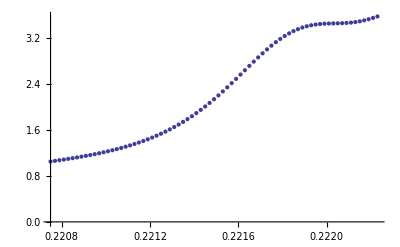

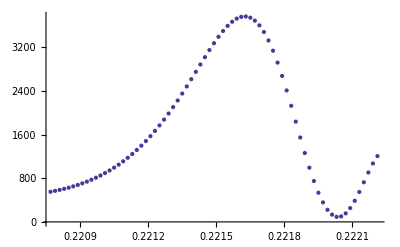

```mathematica
ListPlot[c[64]]
ListPlot[dcdk[64]]
```

```mathematica
(*Do[

dlnM2dk[l]=Table[{En[l][[All,1]][[i]],(M2E[l][[All,2]][[i]]/M2[l][[All,2]][[i]]-En[l][[All,2]][[i]])},{i,1,Length[En[l]]}];
dlnabsMdk[l]=Table[{En[l][[All,1]][[i]],(absME[l][[All,2]][[i]]/absM[l][[All,2]][[i]]-En[l][[All,2]][[i]])},{i,1,Length[En[l]]}];
U[l]=Table[{En[l][[All,1]][[i]],(1-M4[l][[All,2]][[i]]/(3*M2[l][[All,2]][[i]]^2))},{i,1,Length[En[l]]}];


,{l,{8,12,16,24,32,48,64}}]*)
```

```mathematica
(*
Do[
dUdk[l]=Table[{U[l][[All,1]][[i]],(U[l][[All,2]][[i+1]]-U[l][[All,2]][[i]])/(U[l][[All,1]][[i+1]]-U[l][[All,1]][[i]])},{i,1,Length[U[l]]-1}];
,{l,{8,12,16,24,32,48,64}}]
*)
```

```mathematica
(*
Do[
dM2dk[l]=Table[{M2[l][[All,1]][[i]],(M2[l][[All,2]][[i+1]]-M2[l][[All,2]][[i]])/(M2[l][[All,1]][[i+1]]-M2[l][[All,1]][[i]])},{i,1,Length[M2[l]]-1}];
dlnM2dk2[l]=Table[{M2[l][[All,1]][[i]],dM2dk[l][[All,2]][[i]]/M2[l][[All,2]][[i]]},{i,1,Length[M2[l]]-1}];
,{l,{8,12,16,24,32,48,64}}]
*)
```

```mathematica
(*
Do[
dabsMdk[l]=Table[{absM[l][[All,1]][[i]],(absM[l][[All,2]][[i+1]]-absM[l][[All,2]][[i]])/(absM[l][[All,1]][[i+1]]-absM[l][[All,1]][[i]])},{i,1,Length[absM[l]]-1}];
dlnabsMdk2[l]=Table[{absM[l][[All,1]][[i]],dabsMdk[l][[All,2]][[i]]/absM[l][[All,2]][[i]]},{i,1,Length[absM[l]]-1}];
,{l,{8,12,16,24,32,48,64}}]
*)
```

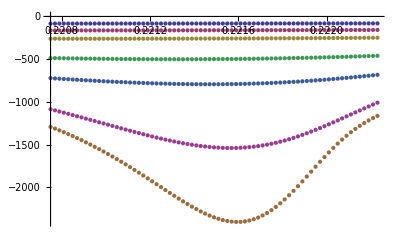

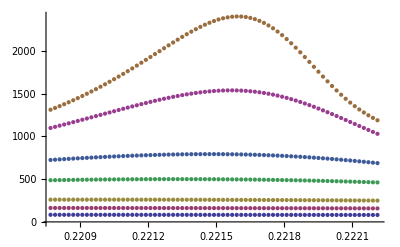

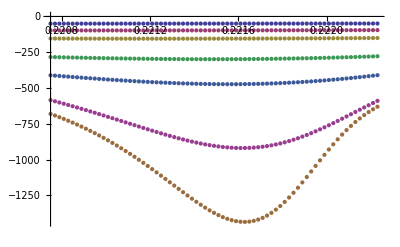

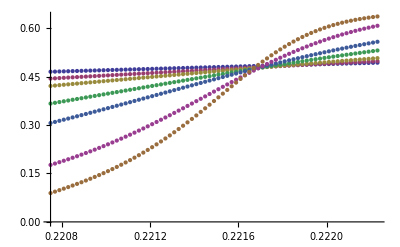

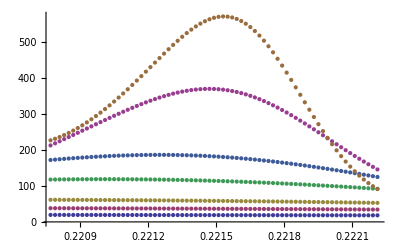

```mathematica
ListPlot[{dlnM2dk[8],dlnM2dk[12],dlnM2dk[16],dlnM2dk[24],dlnM2dk[32],dlnM2dk[48],dlnM2dk[64]}]
ListPlot[{dlnM2dk2[8],dlnM2dk2[12],dlnM2dk2[16],dlnM2dk2[24],dlnM2dk2[32],dlnM2dk2[48],dlnM2dk2[64]}]
ListPlot[{dlnabsMdk[8],dlnabsMdk[12],dlnabsMdk[16],dlnabsMdk[24],dlnabsMdk[32],dlnabsMdk[48],dlnabsMdk[64]}]
ListPlot[{U[8],U[12],U[16],U[24],U[32],U[48],U[64]}]
ListPlot[{dUdk[8],dUdk[12],dUdk[16],dUdk[24],dUdk[32],dUdk[48],dUdk[64]}]
```

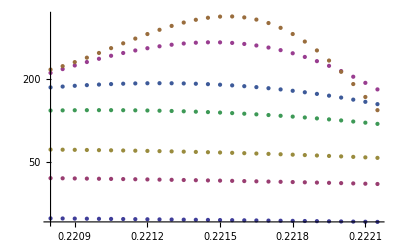

```mathematica
ListLogPlot[{dUdk[8],dUdk[12],dUdk[16],dUdk[24],dUdk[32],dUdk[48],dUdk[64]},PlotRange->Full]
```

```mathematica
maxdlnM2dk=Table[{l,-Max[dlnM2dk[l][[All,2]]]},{l,{8,12,16,24,32,48,64}}]
maxdlnM2dk2=Table[{l,Max[dlnM2dk2[l][[All,2]]]},{l,{8,12,16,24,32,48,64}}]
maxdlnabsMdk=Table[{l,-Max[dlnabsMdk[l][[All,2]]]},{l,{8,12,16,24,32,48,64}}];
maxdlnabsMdk2=Table[{l,Max[dlnabsMdk2[l][[All,2]]]},{l,{8,12,16,24,32,48,64}}];
maxdUdk=Table[{l,Max[dUdk[l][[All,2]]]},{l,{8,12,16,24,32,48,64}}];
LogmaxdlnM2dk=Table[{Log[maxdlnM2dk[[All,1]][[i]]],Log[maxdlnM2dk[[All,2]][[i]]]},{i,1,Length[maxdlnM2dk]}];
LogmaxdlnM2dk2=Table[{Log[maxdlnM2dk2[[All,1]][[i]]],Log[maxdlnM2dk2[[All,2]][[i]]]},{i,1,Length[maxdlnM2dk2]}];
LogmaxdlnabsMdk=Table[{Log[maxdlnabsMdk[[All,1]][[i]]],Log[maxdlnabsMdk[[All,2]][[i]]]},{i,1,Length[maxdlnabsMdk]}];
LogmaxdlnabsMdk2=Table[{Log[maxdlnabsMdk2[[All,1]][[i]]],Log[maxdlnabsMdk2[[All,2]][[i]]]},{i,1,Length[maxdlnabsMdk2]}];
LogmaxdUdk=Table[{Log[maxdUdk[[All,1]][[i]]],Log[maxdUdk[[All,2]][[i]]]},{i,1,Length[maxdUdk]}];
```

{{8,81.2417},{12,157.665},{16,248.867},{24,459.896},{32,682.298},{48,1008.52},{64,1163.03}}

{{8,83.2928},{12,163.249},{16,260.466},{24,500.334},{32,792.923},{48,1538.75},{64,2403.29}}

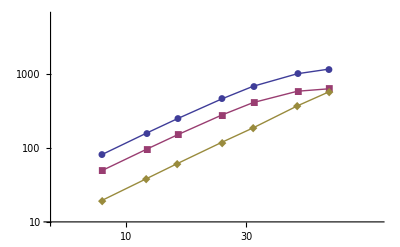

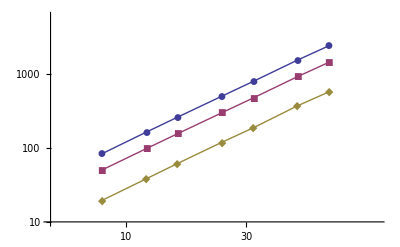

```mathematica
ListLogLogPlot[{maxdlnM2dk,maxdlnabsMdk,maxdUdk},Joined->True,PlotMarkers->Automatic,PlotRange->{{5,100},{10,6000}}]
ListLogLogPlot[{maxdlnM2dk2,maxdlnabsMdk2,maxdUdk},Joined->True,PlotMarkers->Automatic,PlotRange->{{5,100},{10,6000}}]
```

```mathematica
model=a*x+b;

nlf1=NonlinearModelFit[LogmaxdlnM2dk,model,{a,b},x];

nlf1[{"BestFit","ParameterTable"}]

nlf2=NonlinearModelFit[LogmaxdlnM2dk2,model,{a,b},x];

nlf2[{"BestFit","ParameterTable"}]

nlf3=NonlinearModelFit[LogmaxdlnabsMdk,model,{a,b},x];

nlf3[{"BestFit","ParameterTable"}]

nlf4=NonlinearModelFit[LogmaxdlnabsMdk2,model,{a,b},x];

nlf4[{"BestFit","ParameterTable"}]

nlf5=NonlinearModelFit[LogmaxdUdk,model,{a,b},x];

nlf5[{"BestFit","ParameterTable"}]
```

{1.77659+1.32924 x, | Estimate | Standard Error | t-Statistic | P-Value
a | 1.32924 | 0.0814903 | 16.3116 | 0.0000157939
b | 1.77659 | 0.262401 | 6.77054 | 0.00106828}

{1.07149+1.61711 x, | Estimate | Standard Error | t-Statistic | P-Value
a | 1.61711 | 0.0051274 | 315.385 | 6.08204×10^-12
b | 1.07149 | 0.0165104 | 64.8979 | 1.64454×10^-8}

{1.40056+1.28038 x, | Estimate | Standard Error | t-Statistic | P-Value
a | 1.28038 | 0.0935343 | 13.6889 | 0.0000373201
b | 1.40056 | 0.301183 | 4.65021 | 0.00558107}

{0.57099+1.61264 x, | Estimate | Standard Error | t-Statistic | P-Value
a | 1.61264 | 0.00426692 | 377.94 | 2.46125×10^-12
b | 0.57099 | 0.0137396 | 41.558 | 1.52173×10^-7}

{-0.403855+1.62758 x, | Estimate | Standard Error | t-Statistic | P-Value
a | 1.62758 | 0.00793033 | 205.235 | 5.21117×10^-11
b | -0.403855 | 0.0255359 | -15.8152 | 0.0000183867}

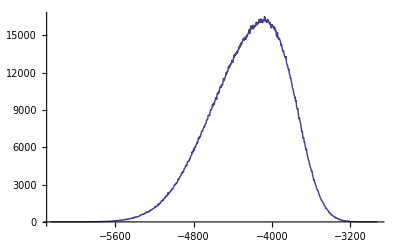

```mathematica
ListLinePlot[his[16]]
```

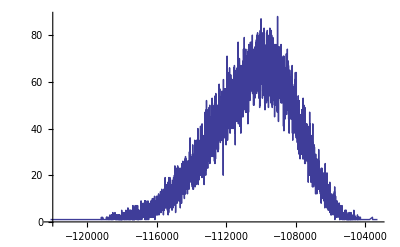

```mathematica
ListLinePlot[his[48]]
```

```mathematica
Do[
m2e[l]=Table[{e[l][[i]],m2[l][[i]]},{i,1,Length[e[l]]}];
,{l,{96}}
]

Do[
m2ee[l]=Table[{e[l][[i]],m2[l][[i]]*e[l][[i]]},{i,1,Length[e[l]]}];
,{l,{96}}
]
```

```mathematica
Do[
m2eh[l]=Table[{e[l][[i]],m2[l][[i]]*e[l][[i]]*his[l][[All,2]][[i]]},{i,1,Length[e[l]]}];
,{l,{96}}
]
```

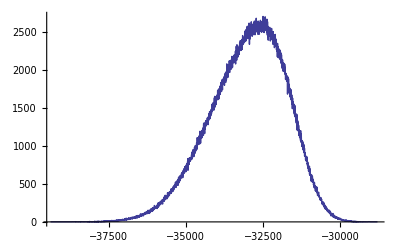

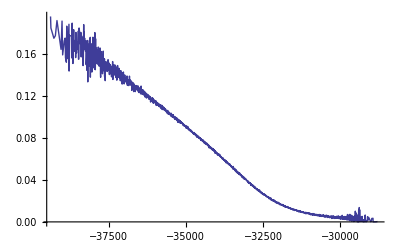

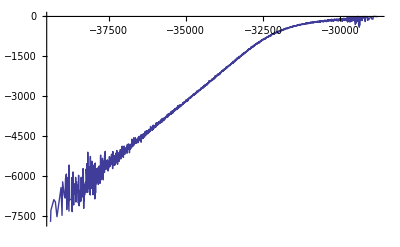

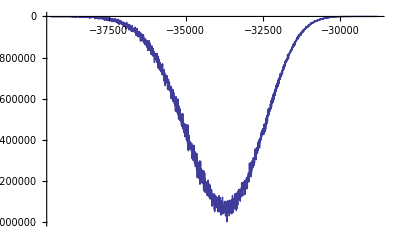

```mathematica
ListLinePlot[his[32]]
ListLinePlot[m2e[32]]
ListLinePlot[m2ee[32]]
ListLinePlot[m2eh[32]]
```

```mathematica
***************************************************************************
```

```mathematica
Do[
dlnM2dka[l]=dlnM2dk[l];
dlnM2dk2a[l]=dlnM2dk2[l];
dlnabsMdk2a[l]=dlnabsMdk2[l];
dlnabsMdka[l]=dlnabsMdk[l];
Ua[l]=U[l];
dUdka[l]=dUdk[l];
ca[l]=c[l];
dcdka[l]=dcdk[l];
absMa[l]=absM[l];
Ena[l]=En[l];
E2a[l]=E2[l];

,{l,{8,12,16,24,32,48,64,96}}]
```

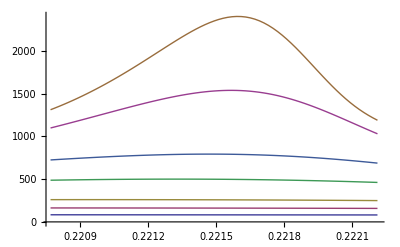

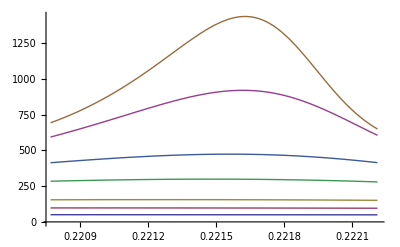

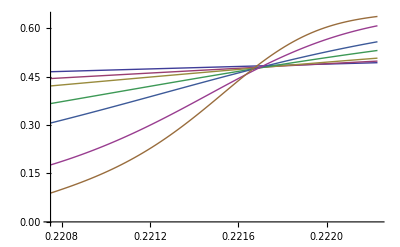

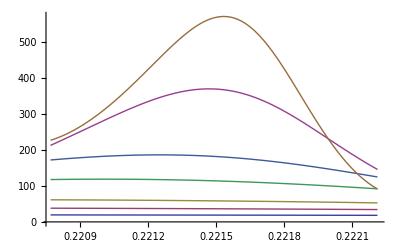

```mathematica
ListLinePlot[{dlnM2dk2[8],dlnM2dk2[12],dlnM2dk2[16],dlnM2dk2[24],dlnM2dk2[32],dlnM2dk2[48],dlnM2dk2[64]}]
ListLinePlot[{dlnabsMdk2[8],dlnabsMdk2[12],dlnabsMdk2[16],dlnabsMdk2[24],dlnabsMdk2[32],dlnabsMdk2[48],dlnabsMdk2[64]}]
ListLinePlot[{U[8],U[12],U[16],U[24],U[32],U[48],U[64]}]
ListLinePlot[{dUdk[8],dUdk[12],dUdk[16],dUdk[24],dUdk[32],dUdk[48],dUdk[64]}]
```

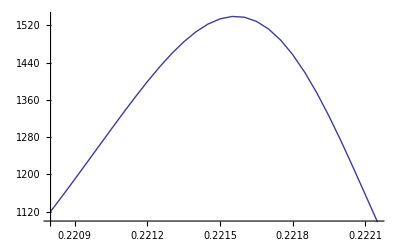

```mathematica
ListLinePlot[{dlnM2dk2[48]}]
```

```mathematica
ν=1/1.6171067787995566;
Do[

dlnabsMdk2s[l]=Table[{dlnabsMdk2[l][[All,1]][[i]],dlnabsMdk2[l][[All,2]][[i]]*l^(-1.6126388223916288)},{i,1,Length[dlnabsMdk2[l]]}];

dlnM2dk2s[l]=Table[{dlnM2dk2[l][[All,1]][[i]],dlnM2dk2[l][[All,2]][[i]]*l^(-1.6171067787995566)},{i,1,Length[dlnM2dk2[l]]}];

dUdks[l]=Table[{dUdk[l][[All,1]][[i]],dUdk[l][[All,2]][[i]]*l^(-1.6275818648561262)},{i,1,Length[dUdk[l]]}]


,{l,{8,12,16,24,32,48,64,96}}]
```

-Graphics-

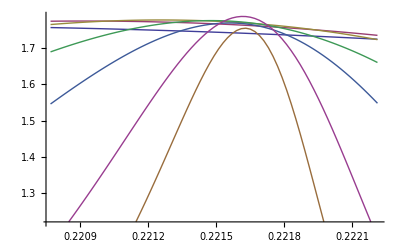

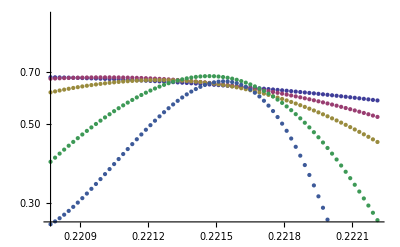

```mathematica
ListLinePlot[{dlnabsMdk2[8],dlnabsMdk2[12],dlnabsMdk2[16],dlnabsMdk2[24],dlnabsMdk2[32],dlnabsMdk2[48],dlnabsMdk2[64]}]
ListLinePlot[{dlnabsMdk2s[8],dlnabsMdk2s[12],dlnabsMdk2s[16],dlnabsMdk2s[24],dlnabsMdk2s[32],dlnabsMdk2s[48],dlnabsMdk2s[64]}]

ListLogPlot[{dUdks[16],dUdks[24],dUdks[32],dUdks[48],dUdks[64]}]
```

```mathematica
Exp[0.5709898101511461]
```

1.77002

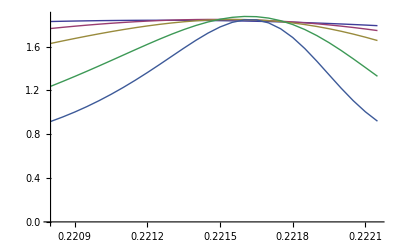

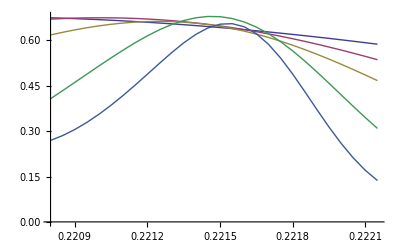

```mathematica
Do[

dlnabsMdk2s[l]=Table[{dlnabsMdk2[l][[All,1]][[i]],dlnabsMdk2[l][[All,2]][[i]]*l^(-1.6)},{i,1,Length[dlnabsMdk2[l]]}];

dlnM2dk2s[l]=Table[{dlnM2dk2[l][[All,1]][[i]],dlnM2dk2[l][[All,2]][[i]]*l^(-1.625)},{i,1,Length[dlnM2dk2[l]]}];

dUdks[l]=Table[{dUdk[l][[All,1]][[i]],dUdk[l][[All,2]][[i]]*l^(-1.6275818648561262)},{i,1,Length[dUdk[l]]}]


,{l,{8,12,16,24,32,48,64,96}}]

ListLinePlot[{dlnabsMdk2s[16],dlnabsMdk2s[24],dlnabsMdk2s[32],dlnabsMdk2s[48],dlnabsMdk2s[64]}]

ListLinePlot[{dUdks[16],dUdks[24],dUdks[32],dUdks[48],dUdks[64]}]
```

```mathematica
maxdlnM2dk=Table[{l,-Max[dlnM2dk[l][[All,2]]]},{l,{24,32,48,64}}];
maxdlnM2dk2=Table[{l,Max[dlnM2dk2[l][[All,2]]]},{l,{24,32,48,64}}]
maxdlnabsMdk=Table[{l,-Max[dlnabsMdk[l][[All,2]]]},{l,{24,32,48,64}}];
maxdlnabsMdk2=Table[{l,Max[dlnabsMdk2[l][[All,2]]]},{l,{24,32,48,64}}];
maxdUdk=Table[{l,Max[dUdk[l][[All,2]]]},{l,{24,32,48,64}}];


LogmaxdlnM2dk=Table[{Log[maxdlnM2dk[[All,1]][[i]]],Log[maxdlnM2dk[[All,2]][[i]]]},{i,1,Length[maxdlnM2dk]}];
LogmaxdlnM2dk2=Table[{Log[maxdlnM2dk2[[All,1]][[i]]],Log[maxdlnM2dk2[[All,2]][[i]]]},{i,1,Length[maxdlnM2dk2]}];
LogmaxdlnabsMdk=Table[{Log[maxdlnabsMdk[[All,1]][[i]]],Log[maxdlnabsMdk[[All,2]][[i]]]},{i,1,Length[maxdlnabsMdk]}];
LogmaxdlnabsMdk2=Table[{Log[maxdlnabsMdk2[[All,1]][[i]]],Log[maxdlnabsMdk2[[All,2]][[i]]]},{i,1,Length[maxdlnabsMdk2]}];
LogmaxdUdk=Table[{Log[maxdUdk[[All,1]][[i]]],Log[maxdUdk[[All,2]][[i]]]},{i,1,Length[maxdUdk]}];


pmaxdUdk=Table[{maxdUdk[[All,1]][[i]],Select[dUdk[maxdUdk[[All,1]][[i]]],#[[2]]==maxdUdk[[All,2]][[i]]&][[All,1]][[1]]},{i,1,Length[maxdUdk]}];
LogpmaxdUdk=Table[{pmaxdUdk[[All,1]][[i]],Log[pmaxdUdk[[All,2]][[i]]]},{i,1,Length[pmaxdUdk]}];

pmaxdlnM2dk2=Table[{maxdlnM2dk2[[All,1]][[i]],Select[dlnM2dk2[maxdlnM2dk2[[All,1]][[i]]],#[[2]]==maxdlnM2dk2[[All,2]][[i]]&][[All,1]][[1]]},{i,1,Length[maxdlnM2dk2]}];
LogpmaxdlnM2dk2=Table[{pmaxdlnM2dk2[[All,1]][[i]],Log[pmaxdlnM2dk2[[All,2]][[i]]]},{i,1,Length[pmaxdlnM2dk2]}];

pmaxdlnabsMdk2=Table[{maxdlnabsMdk2[[All,1]][[i]],Select[dlnabsMdk2[maxdlnabsMdk2[[All,1]][[i]]],#[[2]]==maxdlnabsMdk2[[All,2]][[i]]&][[All,1]][[1]]},{i,1,Length[maxdlnabsMdk2]}];
LogpmaxdlnabsMdk2=Table[{pmaxdlnabsMdk2[[All,1]][[i]],Log[pmaxdlnabsMdk2[[All,2]][[i]]]},{i,1,Length[pmaxdlnabsMdk2]}];

maxdlnM2dka=Table[{l,-Max[dlnM2dka[l][[All,2]]]},{l,{24,32,48,64}}];
maxdlnM2dk2a=Table[{l,Max[dlnM2dk2a[l][[All,2]]]},{l,{24,32,48,64}}]
maxdlnabsMdka=Table[{l,-Max[dlnabsMdka[l][[All,2]]]},{l,{24,32,48,64}}];
maxdlnabsMdk2a=Table[{l,Max[dlnabsMdk2a[l][[All,2]]]},{l,{24,32,48,64}}];
maxdUdka=Table[{l,Max[dUdka[l][[All,2]]]},{l,{24,32,48,64}}];
LogmaxdlnM2dka=Table[{Log[maxdlnM2dka[[All,1]][[i]]],Log[maxdlnM2dka[[All,2]][[i]]]},{i,1,Length[maxdlnM2dka]}];
LogmaxdlnM2dk2a=Table[{Log[maxdlnM2dk2a[[All,1]][[i]]],Log[maxdlnM2dk2a[[All,2]][[i]]]},{i,1,Length[maxdlnM2dk2a]}];
LogmaxdlnabsMdka=Table[{Log[maxdlnabsMdka[[All,1]][[i]]],Log[maxdlnabsMdka[[All,2]][[i]]]},{i,1,Length[maxdlnabsMdka]}];
LogmaxdlnabsMdk2a=Table[{Log[maxdlnabsMdk2a[[All,1]][[i]]],Log[maxdlnabsMdk2a[[All,2]][[i]]]},{i,1,Length[maxdlnabsMdk2a]}];
LogmaxdUdka=Table[{Log[maxdUdka[[All,1]][[i]]],Log[maxdUdka[[All,2]][[i]]]},{i,1,Length[maxdUdka]}];



pmaxdUdka=Table[{maxdUdka[[All,1]][[i]],Select[dUdka[maxdUdka[[All,1]][[i]]],#[[2]]==maxdUdka[[All,2]][[i]]&][[All,1]][[1]]},{i,1,Length[maxdUdka]}];
LogpmaxdUdka=Table[{pmaxdUdka[[All,1]][[i]],Log[pmaxdUdka[[All,2]][[i]]]},{i,1,Length[pmaxdUdka]}];

pmaxdlnM2dk2a=Table[{maxdlnM2dk2a[[All,1]][[i]],Select[dlnM2dk2a[maxdlnM2dk2a[[All,1]][[i]]],#[[2]]==maxdlnM2dk2a[[All,2]][[i]]&][[All,1]][[1]]},{i,1,Length[maxdlnM2dk2a]}];
LogpmaxdlnM2dk2a=Table[{pmaxdlnM2dk2a[[All,1]][[i]],Log[pmaxdlnM2dk2a[[All,2]][[i]]]},{i,1,Length[pmaxdlnM2dk2a]}];

pmaxdlnabsMdk2a=Table[{maxdlnabsMdk2a[[All,1]][[i]],Select[dlnabsMdk2a[maxdlnabsMdk2a[[All,1]][[i]]],#[[2]]==maxdlnabsMdk2a[[All,2]][[i]]&][[All,1]][[1]]},{i,1,Length[maxdlnabsMdk2a]}];
LogpmaxdlnabsMdk2a=Table[{pmaxdlnabsMdk2a[[All,1]][[i]],Log[pmaxdlnabsMdk2a[[All,2]][[i]]]},{i,1,Length[pmaxdlnabsMdk2a]}];
```

{{24,500.334},{32,792.923},{48,1538.75},{64,2403.29}}

{{24,dlnM2dk2a[24]⟦All,2⟧},{32,dlnM2dk2a[32]⟦All,2⟧},{48,dlnM2dk2a[48]⟦All,2⟧},{64,dlnM2dk2a[64]⟦All,2⟧}}

```mathematica
test={{1,2},{2,4},{6,8}};
```

```mathematica
Select[test,#[[2]]==2&][[All,1]]
```

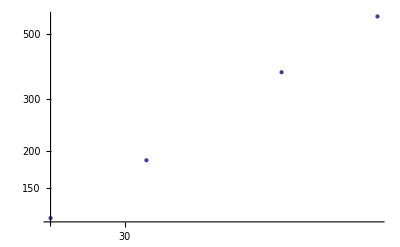

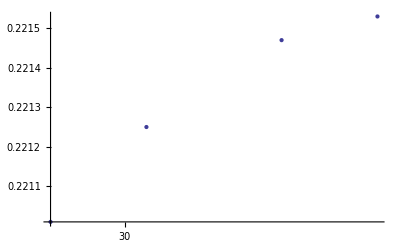

```mathematica
ListLogLogPlot[maxdUdk]
ListLogLogPlot[pmaxdUdk]
```

```mathematica
0.2213125+24^(-2.)
```

0.223049

```mathematica
ClearAll[a,b,d0,α,c0]
model=a*x+b;
model2=d0-c0*x^(-α)

nlf1=NonlinearModelFit[LogmaxdUdk,model,{a,b},x];

nlf1[{"BestFit","ParameterTable"}]

nlf2=NonlinearModelFit[pmaxdUdk,model2,{d0,α,c0},x];

nlf2[{"BestFit","ParameterTable"}]

nlf3=NonlinearModelFit[LogpmaxdUdk,model,{a,b},x];

nlf3[{"BestFit","ParameterTable"}]
```

d0-c0 x^-α

{-0.353457+1.61431 x, | Estimate | Standard Error | t-Statistic | P-Value
a | 1.61431 | 0.023501 | 68.6912 | 0.000211865
b | -0.353457 | 0.0866623 | -4.07856 | 0.0551863}

{0.221666-0.129542/x^1.66226, | Estimate | Standard Error | t-Statistic | P-Value
d0 | 0.221666 | 0.0000628708 | 3525.73 | 0.000180564
α | 1.66226 | 0.32907 | 5.0514 | 0.12442
c0 | 0.129542 | 0.124907 | 1.03711 | 0.488403}

{-1.51054+0.0000564866 x, | Estimate | Standard Error | t-Statistic | P-Value
a | 0.0000564866 | 0.0000147197 | 3.83749 | 0.0616886
b | -1.51054 | 0.000658283 | -2294.67 | 1.89915×10^-7}

```mathematica
Exp[-1.5106529314501942]
```

0.220766

```mathematica
30^(-0.0025193363460768777)
```

0.991468

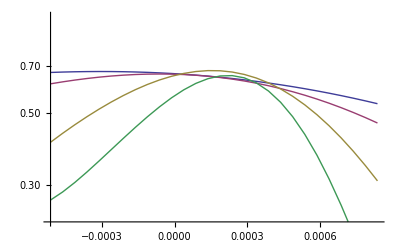

```mathematica
Do[

dlnabsMdk2s[l]=Table[{dlnabsMdk2[l][[All,1]][[i]],dlnabsMdk2[l][[All,2]][[i]]*l^(-1.6)},{i,1,Length[dlnabsMdk2[l]]}];

dlnM2dk2s[l]=Table[{dlnM2dk2[l][[All,1]][[i]],dlnM2dk2[l][[All,2]][[i]]*l^(-1.625)},{i,1,Length[dlnM2dk2[l]]}];

dUdks[l]=Table[{(dUdk[l][[All,1]][[i]]-(0.22131249999999994+l^(-13.250792441944167))),dUdk[l][[All,2]][[i]]*l^(-1.6275818648561262)},{i,1,Length[dUdk[l]]}]


,{l,{8,12,16,24,32,48,64,96}}]

ListLogPlot[{dUdks[24],dUdks[32],dUdks[48],dUdks[64]},Joined->True]
```

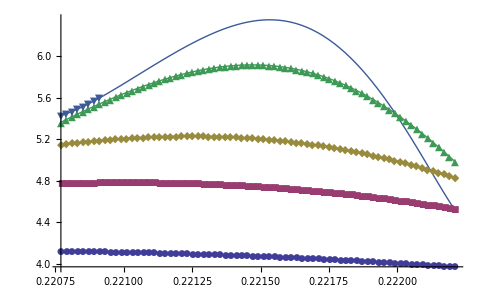

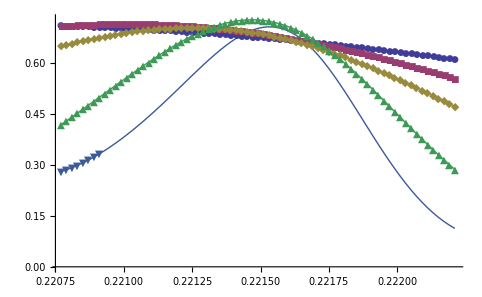

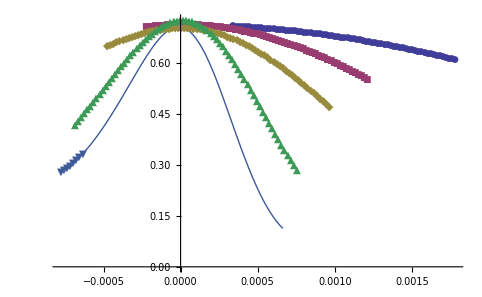

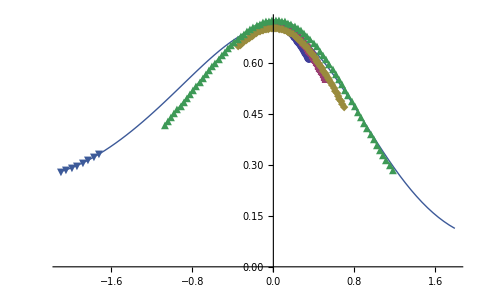

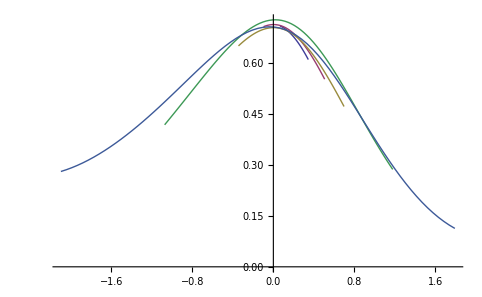

```mathematica
β=1.9;
d0=0.22172269640349793;
α=1.4376787716605537;
ν=1/1.610811561541038;
c=-0.06957573476994093;


Do[

dUdkas1[l]=Table[{dUdka[l][[All,1]][[i]],dUdka[l][[All,2]][[i]]*l^(-1/ν)},{i,1,Length[dUdka[l]]}];

dUdkas2[l]=Table[{(dUdka[l][[All,1]][[i]]-(d0+c*l^(-α))),dUdka[l][[All,2]][[i]]*l^(-1/ν)},{i,1,Length[dUdka[l]]}];


dUdkas[l]=Table[{(dUdka[l][[All,1]][[i]]-(d0+c*l^(-α)))*l^β,dUdka[l][[All,2]][[i]]*l^(-1/ν)},{i,1,Length[dUdka[l]]}]

,{l,{16,24,32,48,64,96}}]

ListLogPlot[{dUdka[16],dUdka[24],dUdka[32],dUdka[48],dUdka[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{dUdkas1[16],dUdkas1[24],dUdkas1[32],dUdkas1[48],dUdkas1[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{dUdkas2[16],dUdkas2[24],dUdkas2[32],dUdkas2[48],dUdkas2[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{dUdkas[16],dUdkas[24],dUdkas[32],dUdkas[48],dUdkas[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{dUdkas[16],dUdkas[24],dUdkas[32],dUdkas[48],dUdkas[64]},Joined->True]
```

```mathematica
ClearAll[a,b,d0,α,c0]
model=a*x+b;
model2=d0-c0*x^(-α)

nlf1=NonlinearModelFit[LogmaxdlnM2dk2,model,{a,b},x];

nlf1[{"BestFit","ParameterTable"}]

nlf2=NonlinearModelFit[pmaxdlnM2dk2,model2,{d0,α,c0},x];

nlf2[{"BestFit","ParameterTable"}]

nlf3=NonlinearModelFit[LogpmaxdlnM2dk2,model,{a,b},x];

nlf3[{"BestFit","ParameterTable"}]
```

d0-c0 x^-α

{1.11524+1.60512 x, | Estimate | Standard Error | t-Statistic | P-Value
a | 1.60512 | 0.0111461 | 144.007 | 0.0000482171
b | 1.11524 | 0.0411026 | 27.1331 | 0.00135556}

{0.221623-0.482328/x^2.32952, | Estimate | Standard Error | t-Statistic | P-Value
d0 | 0.221623 | 0.0000147836 | 14991.2 | 0.0000424663
α | 2.32952 | 0.30416 | 7.65888 | 0.0826542
c0 | 0.482328 | 0.44813 | 1.07631 | 0.476613}

{-1.50854+0.0000275506 x, | Estimate | Standard Error | t-Statistic | P-Value
a | 0.0000275506 | 8.85362×10^-6 | 3.11179 | 0.0896073
b | -1.50854 | 0.000395946 | -3809.95 | 6.88908×10^-8}

```mathematica
maxdlnM2dk2[8]
```

{{24,500.32},{32,792.914},{48,1538.84},{64,2404.2}}[8]

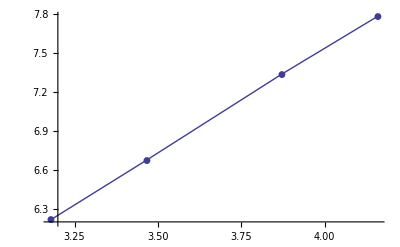

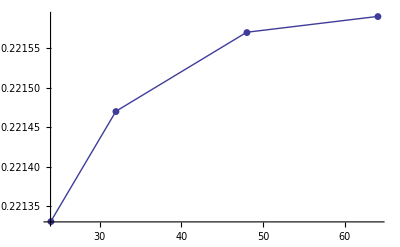

```mathematica
ListLinePlot[{LogmaxdlnM2dk2},PlotMarkers->Automatic]
ListLinePlot[{pmaxdlnM2dk2},PlotMarkers->Automatic]
```

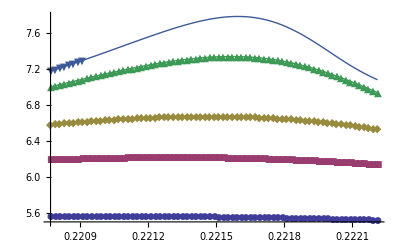

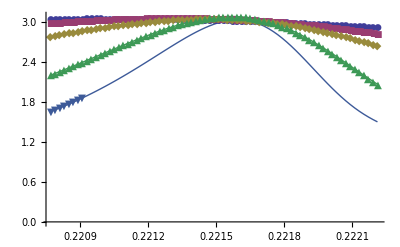

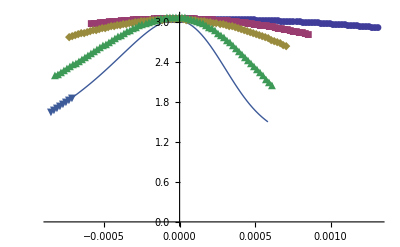

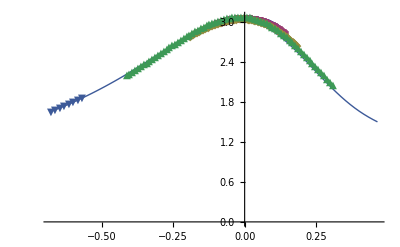

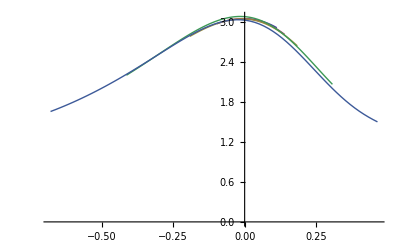

```mathematica
β=1.6055028269228382;
d0=0.22165493296080577;
α=2.329524980715019;
ν=1/1.6055028269228382;
c=-0.4823275484918366;


Do[

dlnM2dk2s1[l]=Table[{dlnM2dk2[l][[All,1]][[i]],dlnM2dk2[l][[All,2]][[i]]*l^(-1/ν)},{i,1,Length[dlnM2dk2[l]]}];

dlnM2dk2s2[l]=Table[{(dlnM2dk2[l][[All,1]][[i]]-(d0+c*l^(-α))),dlnM2dk2[l][[All,2]][[i]]*l^(-1/ν)},{i,1,Length[dlnM2dk2[l]]}];


dlnM2dk2s[l]=Table[{(dlnM2dk2[l][[All,1]][[i]]-(d0+c*l^(-α)))*l^β,dlnM2dk2[l][[All,2]][[i]]*l^(-1/ν)},{i,1,Length[dlnM2dk2[l]]}]

,{l,{16,24,32,48,64}}]

ListLogPlot[{dlnM2dk2[16],dlnM2dk2[24],dlnM2dk2[32],dlnM2dk2[48],dlnM2dk2[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{dlnM2dk2s1[16],dlnM2dk2s1[24],dlnM2dk2s1[32],dlnM2dk2s1[48],dlnM2dk2s1[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{dlnM2dk2s2[16],dlnM2dk2s2[24],dlnM2dk2s2[32],dlnM2dk2s2[48],dlnM2dk2s2[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{dlnM2dk2s[16],dlnM2dk2s[24],dlnM2dk2s[32],dlnM2dk2s[48],dlnM2dk2s[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{dlnM2dk2s[16],dlnM2dk2s[24],dlnM2dk2s[32],dlnM2dk2s[48],dlnM2dk2s[64]},Joined->True]
```

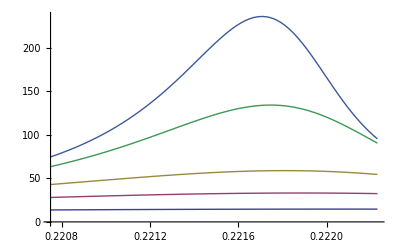

{{8,0.22223},{12,0.22223},{16,0.22205},{24,0.22189},{32,0.22181},{48,0.22175},{64,0.22171}}

d0-c x^-α

{-2.90511+2.01433 x, | Estimate | Standard Error | t-Statistic | P-Value
a | 2.01433 | 0.00398911 | 504.957 | 5.78117×10^-13
b | -2.90511 | 0.012845 | -226.166 | 3.20686×10^-11}

{0.220795+0.00247244/x^0.245977, | Estimate | Standard Error | t-Statistic | P-Value
d0 | 0.220795 | 0.00180412 | 122.384 | 2.67336×10^-8
α | 0.245977 | 0.383617 | 0.641206 | 0.556283
c | -0.00247244 | 0.00101312 | -2.44041 | 0.0711769}

```mathematica
Do[
χ[l]=Table[{M[l][[All,1]][[i]],M[l][[All,1]][[i]]*l^3*(M2[l][[All,2]][[i]]-absM[l][[All,2]][[i]]^2)},{i,1,Length[M[l]]}];
,{l,{8,12,16,24,32,48,64}}]
ListLinePlot[{χ[16],χ[24],χ[32],χ[48],χ[64]},PlotRange->Full]

maxχ=Table[{l,Max[χ[l][[All,2]]]},{l,{8,12,16,24,32,48,64}}];
Logmaxχ=Table[{Log[maxχ[[All,1]][[i]]],Log[maxχ[[All,2]][[i]]]},{i,1,Length[maxχ]}];
pmaxχ=Table[{maxχ[[All,1]][[i]],Select[χ[maxχ[[All,1]][[i]]],#[[2]]==maxχ[[All,2]][[i]]&][[All,1]][[1]]},{i,1,Length[maxχ]}]

ClearAll[a,b,d0,α,c]
model=a*x+b;
model2=d0-c*x^(-α)

nlf1=NonlinearModelFit[Logmaxχ,model,{a,b},x];

nlf1[{"BestFit","ParameterTable"}]

nlf2=NonlinearModelFit[pmaxχ,model2,{d0,α,c},x];

nlf2[{"BestFit","ParameterTable"}]
```

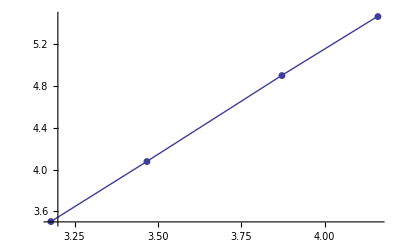

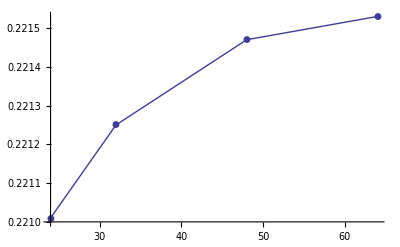

```mathematica
ListLinePlot[{Logmaxχ},PlotMarkers->Automatic]
ListLinePlot[{pmaxχ},PlotMarkers->Automatic]
```

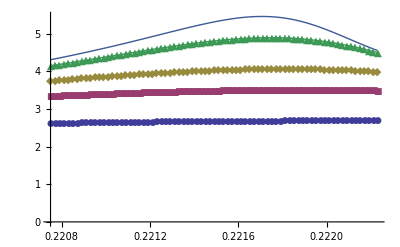

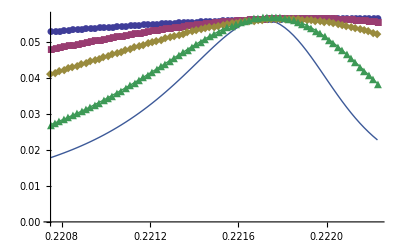

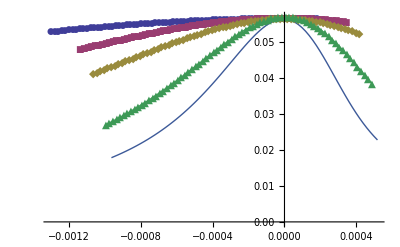

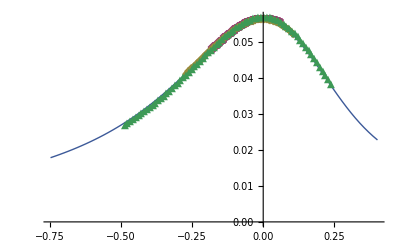

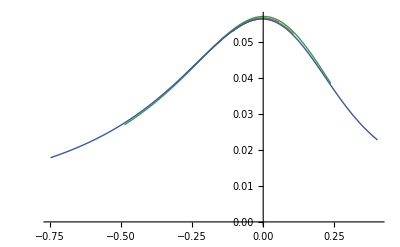

```mathematica
β=1.6;
d0=0.2216379840812124;
α=1.2336631004936391;
ν=1/2.004938606356056;
c=0.012647708332413366;


Do[
χs1[l]=Table[{χ[l][[All,1]][[i]],χ[l][[All,2]][[i]]*l^(-1/ν)},{i,1,Length[χ[l]]}];

χs2[l]=Table[{(χ[l][[All,1]][[i]]-(d0+c*l^(-α))),χ[l][[All,2]][[i]]*l^(-1/ν)},{i,1,Length[χ[l]]}];


χs[l]=Table[{(χ[l][[All,1]][[i]]-(d0+c*l^(-α)))*l^β,χ[l][[All,2]][[i]]*l^(-1/ν)},{i,1,Length[χ[l]]}]

,{l,{16,24,32,48,64}}]

ListLogPlot[{χ[16],χ[24],χ[32],χ[48],χ[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{χs1[16],χs1[24],χs1[32],χs1[48],χs1[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{χs2[16],χs2[24],χs2[32],χs2[48],χs2[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{χs[16],χs[24],χs[32],χs[48],χs[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{χs[16],χs[24],χs[32],χs[48],χs[64]},Joined->True]
```

```mathematica
Do[

c[l]={};



c[l]=Table[{En[l][[All,1]][[i]],En[l][[All,1]][[i]]^2*(E2[l][[All,2]][[i]]-En[l][[All,2]][[i]]^2)},{i,1,Length[En[l]]}];

dE2dk[l]=Table[{E2[l][[All,1]][[i]],(E2[l][[All,2]][[i+1]]-E2[l][[All,2]][[i-1]])/(E2[l][[All,1]][[i+1]]-E2[l][[All,1]][[i-1]])},{i,2,Length[E2[l]]-1}];


,{l,{8,12,16,24,32,48,64}}]
```

```mathematica
maxdcdk=Table[{l,Max[dcdk[l][[All,2]]]},{l,{8,12,16,24,32,48,64}}];
Logmaxdcdk=Table[{Log[maxdcdk[[All,1]][[i]]],Log[maxdcdk[[All,2]][[i]]]},{i,1,Length[maxdcdk]}];
pmaxdcdk=Table[{maxdcdk[[All,1]][[i]],Select[dcdk[maxdcdk[[All,1]][[i]]],#[[2]]==maxdcdk[[All,2]][[i]]&][[All,1]][[1]]},{i,1,Length[maxdcdk]}];
vcpmaxdcdk=Table[{pmaxdcdk[[All,1]][[i]],Select[c[pmaxdcdk[[All,1]][[i]]],#[[1]]==pmaxdcdk[[All,2]][[i]]&][[All,2]][[1]]},{i,1,Length[maxdcdk]}];
Logvcpmaxdcdk=Table[{Log[vcpmaxdcdk[[All,1]][[i]]],Log[vcpmaxdcdk[[All,2]][[i]]]},{i,1,Length[vcpmaxdcdk]}];


ClearAll[a,b,d0,α,c0]
model=a*x-b;
model2=d0-c0*x^(-α)

nlf1=NonlinearModelFit[Logmaxdcdk,model,{a,b},x];

nlf1[{"BestFit","ParameterTable"}]

nlf3=NonlinearModelFit[Logvcpmaxdcdk,model,{a,b},x];

nlf3[{"BestFit","ParameterTable"}]


nlf2=NonlinearModelFit[pmaxdcdk,model2,{d0,α,c0},x];

nlf2[{"BestFit","ParameterTable"}]
```

d0-c0 x^-α

{0.701232+1.81677 x, | Estimate | Standard Error | t-Statistic | P-Value
a | 1.81677 | 0.00849589 | 213.841 | 4.24376×10^-11
b | -0.701232 | 0.027357 | -25.6326 | 1.68765×10^-6}

{-0.408736+3.33787 x, | Estimate | Standard Error | t-Statistic | P-Value
a | 3.33787 | 0.010567 | 315.876 | 6.03497×10^-12
b | 0.408736 | 0.0340261 | 12.0124 | 0.0000705396}

{0.221722-0.0160547/x^1.35023, | Estimate | Standard Error | t-Statistic | P-Value
d0 | 0.221722 | 0.0000508372 | 4361.41 | 1.65823×10^-14
α | 1.35023 | 0.205067 | 6.58432 | 0.00275493
c0 | 0.0160547 | 0.00643929 | 2.49325 | 0.0672505}

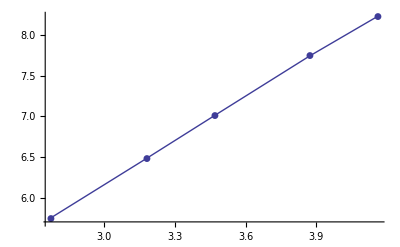

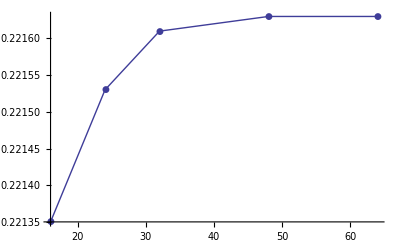

```mathematica
ListLinePlot[{Logmaxdcdk},PlotMarkers->Automatic]
ListLinePlot[{pmaxdcdk},PlotMarkers->Automatic]
```

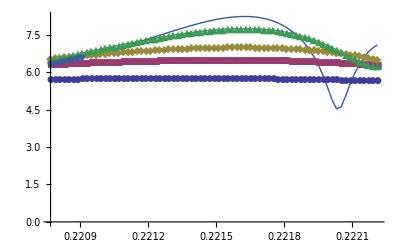

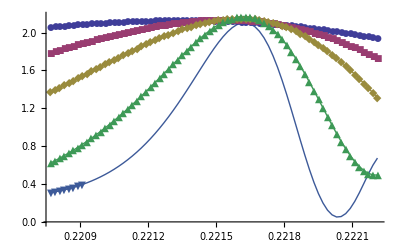

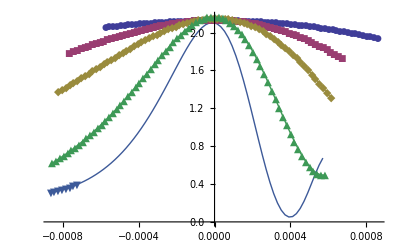

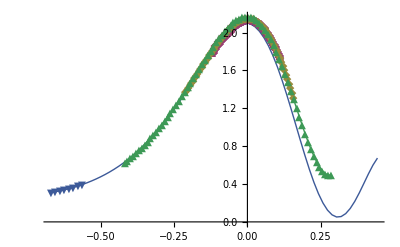

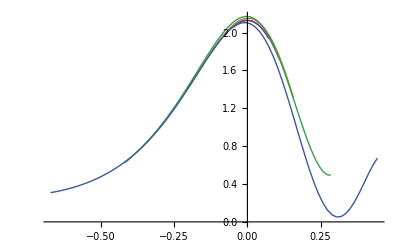

```mathematica
β=1.6;
d0=0.22164563555955621;
α=2.5680900383116363;
ν=1/1.8008626010649404;
c0=-0.36741884510301914;


Do[
dcdks1[l]=Table[{dcdk[l][[All,1]][[i]],dcdk[l][[All,2]][[i]]*l^(-1/ν)},{i,1,Length[dcdk[l]]}];

dcdks2[l]=Table[{(dcdk[l][[All,1]][[i]]-(d0+c0*l^(-α))),dcdk[l][[All,2]][[i]]*l^(-1/ν)},{i,1,Length[dcdk[l]]}];


dcdks[l]=Table[{(dcdk[l][[All,1]][[i]]-(d0+c0*l^(-α)))*l^β,dcdk[l][[All,2]][[i]]*l^(-1/ν)},{i,1,Length[dcdk[l]]}]

,{l,{16,24,32,48,64}}]
ListLogPlot[{dcdk[16],dcdk[24],dcdk[32],dcdk[48],dcdk[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{dcdks1[16],dcdks1[24],dcdks1[32],dcdks1[48],dcdks1[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{dcdks2[16],dcdks2[24],dcdks2[32],dcdks2[48],dcdks2[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{dcdks[16],dcdks[24],dcdks[32],dcdks[48],dcdks[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{dcdks[16],dcdks[24],dcdks[32],dcdks[48],dcdks[64]},Joined->True]
```

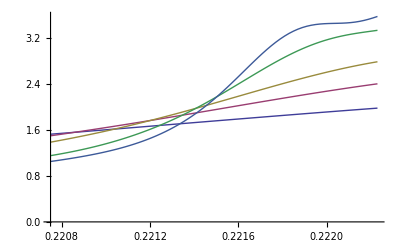

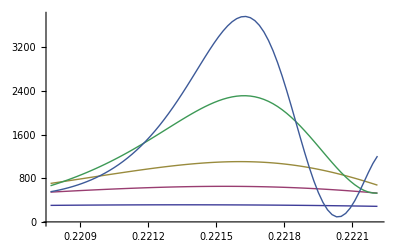

```mathematica
ListLinePlot[{c[16],c[24],c[32],c[48],c[64]}]
ListLinePlot[{dcdk[16],dcdk[24],dcdk[32],dcdk[48],dcdk[64]}]
```

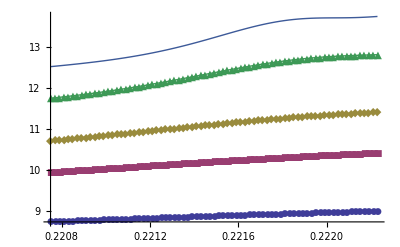

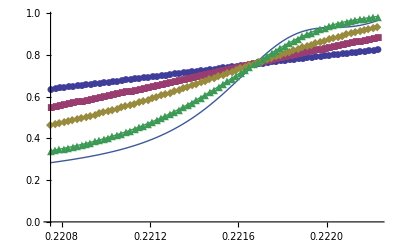

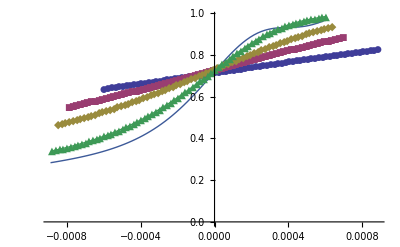

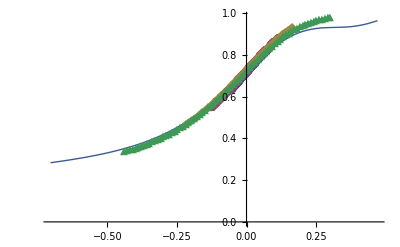

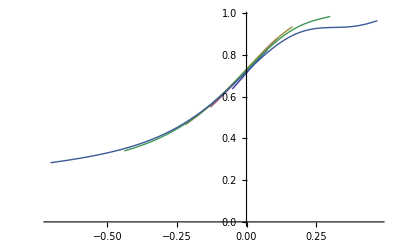

```mathematica
β=1.6055028269228382;
d0=0.22164563555955621;
α=2.5680900383116363;
ν=1/3.314498452808983;
c0=-0.36741884510301914;


Do[


cs1[l]=Table[{(c[l][[All,1]][[i]]),c[l][[All,2]][[i]]*l^(-1/ν)},{i,1,Length[c[l]]}];




cs2[l]=Table[{(c[l][[All,1]][[i]]-(d0+c0*l^(-α))),c[l][[All,2]][[i]]*l^(-1/ν)},{i,1,Length[c[l]]}];

cs[l]=Table[{(c[l][[All,1]][[i]]-(d0+c0*l^(-α)))*l^β,c[l][[All,2]][[i]]*l^(-1/ν)},{i,1,Length[c[l]]}];

,{l,{16,24,32,48,64}}]
ListLogPlot[{c[16],c[24],c[32],c[48],c[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{cs1[16],cs1[24],cs1[32],cs1[48],cs1[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{cs2[16],cs2[24],cs2[32],cs2[48],cs2[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{cs[16],cs[24],cs[32],cs[48],cs[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{cs[16],cs[24],cs[32],cs[48],cs[64]},Joined->True]
```

```mathematica
ClearAll[c]
```

```mathematica
maxdcdk=Table[{l,Max[dcdk[l][[All,2]]]},{l,{8,12,16,24,32,48,64,96}}]
Logmaxdcdk=Table[{Log[maxdcdk[[All,1]][[i]]],Log[maxdcdk[[All,2]][[i]]]},{i,1,Length[maxdcdk]}]
pmaxdcdk=Table[{maxdcdk[[All,1]][[i]],Select[dcdk[maxdcdk[[All,1]][[i]]],#[[2]]==maxdcdk[[All,2]][[i]]&][[All,1]][[1]]},{i,1,Length[maxdcdk]}]
vcpmaxdcdk=Table[{pmaxdcdk[[All,1]][[i]],Select[c[pmaxdcdk[[All,1]][[i]]],#[[1]]==pmaxdcdk[[All,2]][[i]]&][[All,2]][[1]]},{i,1,Length[maxdcdk]}]
```

{{8,86.6198},{12,185.174},{16,313.321},{24,651.924},{32,1104.75},{48,2312.52},{64,3765.74},{96,1.65087×10^6}}

{{Log[8],4.46153},{Log[12],5.2213},{Log[16],5.74723},{Log[24],6.47993},{Log[32],7.00737},{Log[48],7.74609},{Log[64],8.2337},{Log[96],14.3168}}

{{8,0.22077},{12,0.22111},{16,0.22135},{24,0.22153},{32,0.22161},{48,0.22163},{64,0.22163},{96,0.22151}}

{{8,675.594},{12,2645.92},{16,7001.45},{24,27274.7},{32,71886.6},{48,272548.},{64,690832.},{96,c[]⟦1⟧}}

```mathematica
pmaxdcdk[[All,1]]
```

{16,24,32,48,64}

```mathematica
0.3144984528089845/1.6
```

0.196562

```mathematica
2.004938606356056/1.6
```

1.25309

```mathematica
1/1.6
```

0.625

```mathematica
1.6/1.8008626010649404
```

0.888463

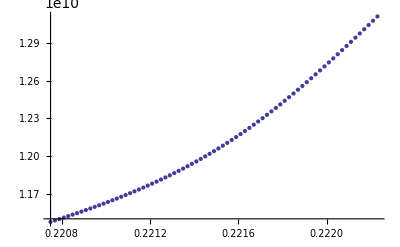

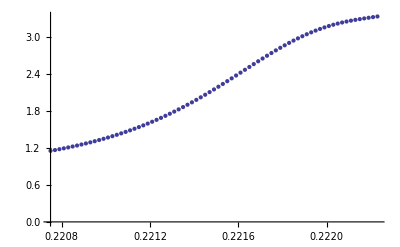

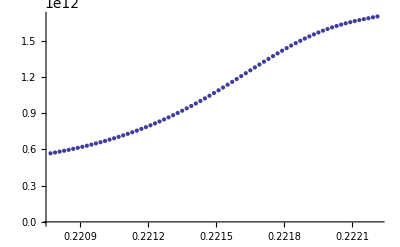

```mathematica
ListPlot[E2[48]]
ListPlot[c[48]]
ListPlot[dE2dk[48]]
```

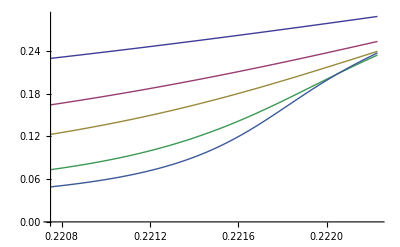

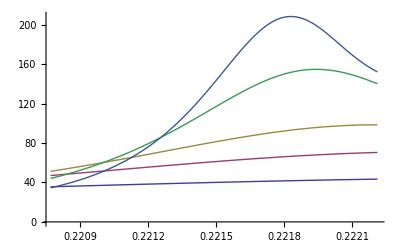

```mathematica
ListLinePlot[{absM[16],absM[24],absM[32],absM[48],absM[64]}]
ListLinePlot[{dabsMdk[16],dabsMdk[24],dabsMdk[32],dabsMdk[48],dabsMdk[64]}]
```

```mathematica
maxdabsMdk=Table[{l,Max[dabsMdk[l][[All,2]]]},{l,{16,24,32,48,64}}];
LogmaxdabsMdk=Table[{Log[maxdabsMdk[[All,1]][[i]]],Log[maxdabsMdk[[All,2]][[i]]]},{i,1,Length[maxdabsMdk]}]
pmaxdabsMdk=Table[{maxdabsMdk[[All,1]][[i]],Select[dabsMdk[maxdabsMdk[[All,1]][[i]]],#[[2]]==maxdabsMdk[[All,2]][[i]]&][[All,1]][[1]]},{i,1,Length[maxdabsMdk]}]
vabsMpmaxdabsMdk=Table[{pmaxdabsMdk[[All,1]][[i]],Select[absM[pmaxdabsMdk[[All,1]][[i]]],#[[1]]==pmaxdabsMdk[[All,2]][[i]]&][[All,2]][[1]]},{i,1,Length[pmaxdabsMdk]}]
LogvabsmpmaxdabsMdk=Table[{Log[vabsMpmaxdabsMdk[[All,1]][[i]]],Log[vabsMpmaxdabsMdk[[All,2]][[i]]]},{i,1,Length[vabsMpmaxdabsMdk]}]

ClearAll[a,b,d0,α,c0]
model=a*x-b;
model2=d0+c0*x^(-α)

nlf1=NonlinearModelFit[LogmaxdabsMdk,model,{a,b},x];

nlf1[{"BestFit","ParameterTable"}]

nlf3=NonlinearModelFit[LogvabsmpmaxdabsMdk,model,{a,b},x];

nlf3[{"BestFit","ParameterTable"}]


nlf2=NonlinearModelFit[pmaxdabsMdk,model2,{d0,α,c0},x];

nlf2[{"BestFit","ParameterTable"}]
```

{{Log[16],3.80877},{Log[24],4.26654},{Log[32],4.58888},{Log[48],5.04109},{Log[64],5.33889}}

{{16,0.22313},{24,0.22249},{32,0.22221},{48,0.22195},{64,0.22183}}

{{16,0.328694},{24,0.271961},{32,0.237668},{48,0.192726},{64,0.16468}}

{{Log[16],-1.11263},{Log[24],-1.3021},{Log[32],-1.43688},{Log[48],-1.64649},{Log[64],-1.80375}}

d0+c0 x^-α

{0.745973+1.10706 x, | Estimate | Standard Error | t-Statistic | P-Value
a | 1.10706 | 0.00913917 | 121.134 | 1.24042×10^-6
b | -0.745973 | 0.0322034 | -23.1645 | 0.000176238}

{0.276744-0.497841 x, | Estimate | Standard Error | t-Statistic | P-Value
a | -0.497841 | 0.00981484 | -50.7233 | 0.0000168749
b | -0.276744 | 0.0345842 | -8.00204 | 0.00407358}

{0.221574+0.0566599/x^1.29684, | Estimate | Standard Error | t-Statistic | P-Value
d0 | 0.221574 | 0.0000105924 | 20918.1 | 2.28536×10^-9
α | 1.29684 | 0.0189413 | 68.4661 | 0.00021326
c0 | 0.0566599 | 0.00266803 | 21.2366 | 0.00220999}

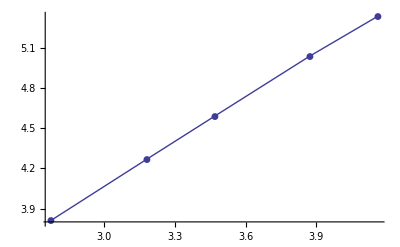

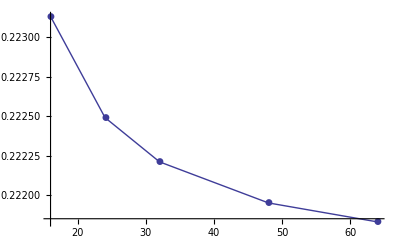

```mathematica
ListLinePlot[{LogmaxdabsMdk},PlotMarkers->Automatic]
ListLinePlot[{pmaxdabsMdk},PlotMarkers->Automatic]
```

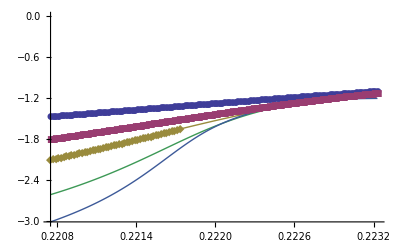

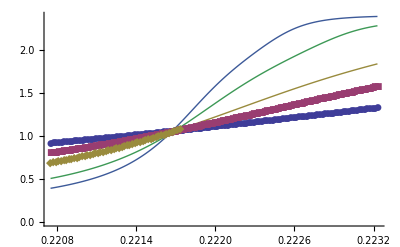

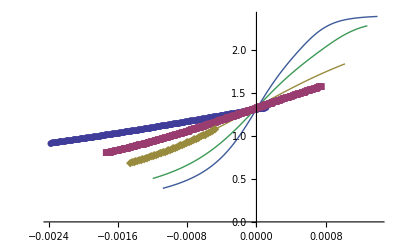

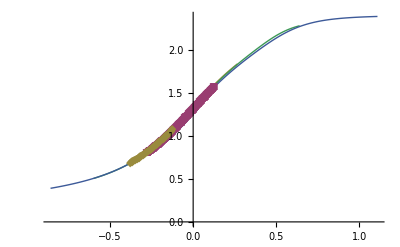

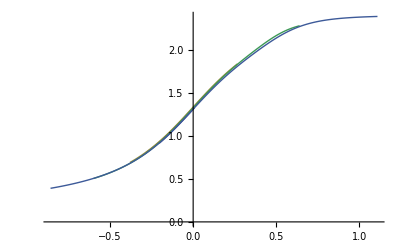

```mathematica
b=1.6051220837004385;
k0=0.22157425838830616;
d=-1.2968371659073874;
a=-0.497840946648326;
c0=0.05665990466313132;


Do[


absMs1[l]=Table[{(absM[l][[All,1]][[i]]),absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];




absMs2[l]=Table[{(absM[l][[All,1]][[i]]-(k0+c0*l^(d))),absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];

absMs[l]=Table[{(absM[l][[All,1]][[i]]-(k0+c0*l^(d)))*l^b,absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];

absMs[l]=Table[{(absM[l][[All,1]][[i]]-(k0+c0*l^(d)))*l^b,absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];

,{l,{16,24,32,48,64}}]
ListLogPlot[{absM[16],absM[24],absM[32],absM[48],absM[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{absMs1[16],absMs1[24],absMs1[32],absMs1[48],absMs1[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{absMs2[16],absMs2[24],absMs2[32],absMs2[48],absMs2[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{absMs[16],absMs[24],absMs[32],absMs[48],absMs[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{absMs[16],absMs[24],absMs[32],absMs[48],absMs[64]},Joined->True]
```

-Graphics-

-Graphics-

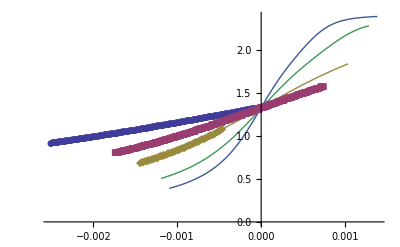

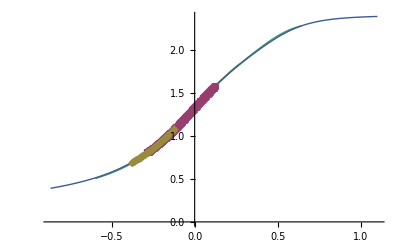

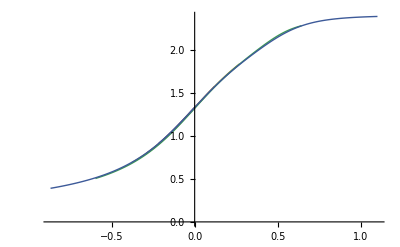

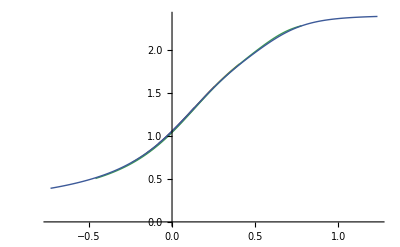

```mathematica
b=1.6051220837004385;
k0=0.22167153966634826;
d=-b;
a=-0.497840946648326;
c0=0.13617622065774748;


Do[


absMs1[l]=Table[{(absM[l][[All,1]][[i]]),absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];




absMs2[l]=Table[{(absM[l][[All,1]][[i]]-(k0+c0*l^(d))),absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];

absMs[l]=Table[{(absM[l][[All,1]][[i]]-(k0+c0*l^(d)))*l^b,absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];


absMs3[l]=Table[{(absM[l][[All,1]][[i]]-k0)*l^b,absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];

,{l,{16,24,32,48,64}}]
ListLogPlot[{absM[16],absM[24],absM[32],absM[48],absM[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{absMs1[16],absMs1[24],absMs1[32],absMs1[48],absMs1[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{absMs2[16],absMs2[24],absMs2[32],absMs2[48],absMs2[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{absMs[16],absMs[24],absMs[32],absMs[48],absMs[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{absMs[16],absMs[24],absMs[32],absMs[48],absMs[64]},Joined->True]

ListPlot[{absMs3[16],absMs3[24],absMs3[32],absMs3[48],absMs3[64]},Joined->True]
```

```mathematica
------------------------
```

```mathematica
β=1.6055028269228382;
d0=0.22165493296080577;
α=2.329524980715019;
ν=1/1.6055028269228382;
c=-0.4823275484918366;


Do[

dlnM2dk2s1[l]=Table[{dlnM2dk2[l][[All,1]][[i]],dlnM2dk2[l][[All,2]][[i]]*l^(-1/ν)},{i,1,Length[dlnM2dk2[l]]}];

dlnM2dk2s2[l]=Table[{(dlnM2dk2[l][[All,1]][[i]]-(d0+c*l^(-α))),dlnM2dk2[l][[All,2]][[i]]*l^(-1/ν)},{i,1,Length[dlnM2dk2[l]]}];


dlnM2dk2s[l]=Table[{(dlnM2dk2[l][[All,1]][[i]]-(d0+c*l^(-α)))*l^β,dlnM2dk2[l][[All,2]][[i]]*l^(-1/ν)},{i,1,Length[dlnM2dk2[l]]}]

,{l,{16,24,32,48,64}}]

ListLogPlot[{dlnM2dk2[16],dlnM2dk2[24],dlnM2dk2[32],dlnM2dk2[48],dlnM2dk2[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{dlnM2dk2s1[16],dlnM2dk2s1[24],dlnM2dk2s1[32],dlnM2dk2s1[48],dlnM2dk2s1[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{dlnM2dk2s2[16],dlnM2dk2s2[24],dlnM2dk2s2[32],dlnM2dk2s2[48],dlnM2dk2s2[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{dlnM2dk2s[16],dlnM2dk2s[24],dlnM2dk2s[32],dlnM2dk2s[48],dlnM2dk2s[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{dlnM2dk2s[16],dlnM2dk2s[24],dlnM2dk2s[32],dlnM2dk2s[48],dlnM2dk2s[64]},Joined->True]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

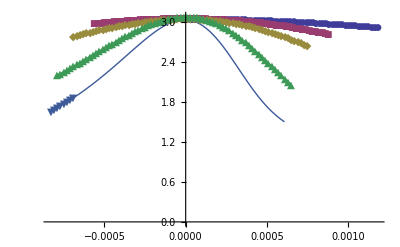

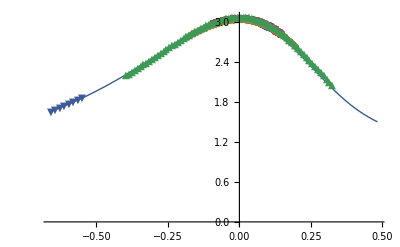

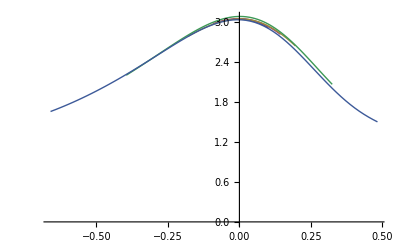

```mathematica
β=1.6055028269228382;
d0=0.22167124258718024;
α=1.6055028269228382;
ν=1/1.6055028269228382;
c=-0.055034812875252054;


Do[

dlnM2dk2s1[l]=Table[{dlnM2dk2[l][[All,1]][[i]],dlnM2dk2[l][[All,2]][[i]]*l^(-1/ν)},{i,1,Length[dlnM2dk2[l]]}];

dlnM2dk2s2[l]=Table[{(dlnM2dk2[l][[All,1]][[i]]-(d0+c*l^(-α))),dlnM2dk2[l][[All,2]][[i]]*l^(-1/ν)},{i,1,Length[dlnM2dk2[l]]}];


dlnM2dk2s[l]=Table[{(dlnM2dk2[l][[All,1]][[i]]-(d0+c*l^(-α)))*l^β,dlnM2dk2[l][[All,2]][[i]]*l^(-1/ν)},{i,1,Length[dlnM2dk2[l]]}]

,{l,{16,24,32,48,64}}]

ListLogPlot[{dlnM2dk2[16],dlnM2dk2[24],dlnM2dk2[32],dlnM2dk2[48],dlnM2dk2[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{dlnM2dk2s1[16],dlnM2dk2s1[24],dlnM2dk2s1[32],dlnM2dk2s1[48],dlnM2dk2s1[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{dlnM2dk2s2[16],dlnM2dk2s2[24],dlnM2dk2s2[32],dlnM2dk2s2[48],dlnM2dk2s2[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{dlnM2dk2s[16],dlnM2dk2s[24],dlnM2dk2s[32],dlnM2dk2s[48],dlnM2dk2s[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{dlnM2dk2s[16],dlnM2dk2s[24],dlnM2dk2s[32],dlnM2dk2s[48],dlnM2dk2s[64]},Joined->True]
```